### Fourier Transform of sine - Gaussian

Define Functions

```mathematica
sineGaussian[t_]:=A ⅇ^(-Γ t^2)Sin[2π Subscript[f, c] t]
```

```mathematica
FT[f_]:=Abs[1/(√T)∫_0^T (sineGaussian[t] ⅇ^(2π f ⅈ t))ⅆt]
```

Define constants

```mathematica
T=1;Subscript[f, c]=1*^3;Q=1;Γ=(2 π Subscript[f, c])/Q^2;A=1*^6;
```

Plot  time-series

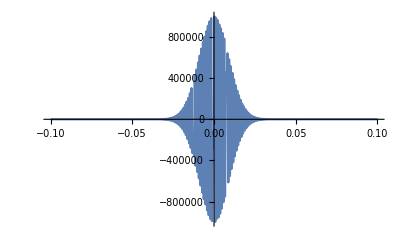

```mathematica
Plot[sineGaussian[t],{t,-0.1,0.1},PlotRange->All]
```

If I copy the output of typing FT[f] and turn it into a new function, and plot the new function, it is significantly faster than just plotting FT[g] - this takes much longer.

Plot Fourier Transform

```mathematica
LogLogPlot[Evaluate[FT[f]],{f,0.01,10^5},PlotRange->Full]
```

General::munfl: Exp[-1570.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4716.9-6283.59 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4716.84+6283.71 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-